## Shallow Flow Moment Equations (periodic in x)

## Function Definitions

### Tools

```mathematica
Clear["Global`*"]

SetAttributes[{P,A0},Listable]
ZeroMatrix[n_]:=0IdentityMatrix[n]
Diag[list_]:=DiagonalMatrix[list]

interpolate[pts_,val_,dim_]:=Block[{len=Length[Flatten[val]]},
Interpolation[ArrayReshape[Flatten[Thread[{ArrayReshape[Flatten[pts],{len,dim}],Flatten[val]}]],{len,dim+1}],InterpolationOrder->1]
]
iSize=400;
color={Red,Green,Blue,Purple};
markers={▲,■,◆,●,★};
```

### Cell Interface Reconstruction

```mathematica
gam=1.5;
Rlimit[dm_,dp_]=If[dp dm≤0,0,Sign[dp]Min[Abs[gam dm],Abs[(2dp+dm)/3],Abs[(1+gam)/2 dp]]]; (*Limiter*)
Rfull[dm_,dp_]=Sign[dp]Max[0,Min[Sign[dp](2dp+dm)/3,Max[-Sign[dp]dm,Min[gam Sign[dp]dm,Sign[dp](2dp+dm)/3,(1+gam)/2 Abs[dp]]]]];

Recon[list_,opt_]:=Map[Map[Function[{um,u,up},{u+1/2 Rlimit[u-um,up-u],u-1/2 Rlimit[up-u,u-um]}]@@#&,Partition[ArrayPad[#,2,opt,InterpolationOrder->1],3,1]]&,list]
(*Recon[list_,opt_]:=Map[Map[Function[{um,u,up},{u,u}]@@#&,Partition[ArrayPad[#,2,opt,InterpolationOrder->1],3,1]]&,list]*)
```

### Full Grid Flux Calculation

```mathematica
Residuum[U_]:=Block[{Urecons1,Uright1,Uleft1,CMax,delta=0.95},
Urecons=Recon[U,"Periodic"];

(* right side of element *)
Uright=Urecons⟦All,;;-2,1⟧;
(* left side of element *)
Uleft=Urecons⟦All,2;;,2⟧;
(* jumps *)
dU=Uright⟦All,2;;⟧-Uleft⟦All,;;-2⟧;

CMax=ConstantArray[ListConvolve[{1/2,1/2},MaxSpeed@@U,{1,-1},"Periodic"],Length[U]];
cMax=Max[CMax];

-1/dx Differences[1/2(Flux@@Uright+Flux@@Uleft)+delta/2 CMax(Uright-Uleft),{0,1}]+1/dx Transpose[MapThread[#1.#2&,{A0@@U,Transpose[dU]}]]-Transpose[P@@U]
]
```

### Simulation Setup and Time Integration

```mathematica
FiniteVolumeRun[nx_,tend_]:=Block[{H1,HU1,H2,HU2},
dx=(x2-x1)/nx;
xs[i_]=x1+(i-0.5)dx;

pts=Table[xs[i],{i,1,nx}];

Uraw=Transpose[Table[init[xs[i]],{i,1,nx}]];

cMax=0.0;
dt=0.1dx;
time=0.0;
step=0;

While[time<tend,

(*U1=Uraw+dt Residuum[Uraw];

U2=3/4 Uraw+1/4(U1+dt Residuum[U1]);

Uraw=1/3 Uraw+2/3(U2+dt Residuum[U2]);*)

Uraw=Uraw+dt Residuum[Uraw];

time+=dt;
step++;

(*dt=0.995dx/cMax;*)
dt=0.1dx/cMax;
CFL=cMax dt/dx;
If[time+dt≥tend&&time<tend,dt=tend-time+10^-8];
];

{time,step}
];
```

### Visualization for Dynamic Output

```mathematica
Visual[U_,iSize_]:=Block[{nx,ny},

Grid[{{
Show[Plot[0,{x,x1,x2},GridLines->{{-0.5,0,0.5},{}},PlotLabel->"h(x,t) at time: "<>ToString[time]<>" (step: "<>ToString[step]<>", Δt = "<>ToString[dt]<>", CFL = "<>ToString[CFL]<>")",PlotRange->{{x1,x2},{0.8,1.5}},Frame->True,ImageSize->iSize,Epilog->{Inset[Panel[modeltag],Scaled[{.9,.9}]]}],
ListPlot[Transpose[{pts,U⟦1⟧}],ImageSize->iSize]],
Show[Plot[{0},{x,x1,x2},GridLines->{{-0.5,0,0.5},{}},PlotStyle->{Red,Blue,Green},PlotLabel->"u_Ave(x,t)",PlotRange->{{x1,x2},{-0.4,0.6}},Frame->True,ImageSize->iSize,Epilog->{Inset[Panel[modeltag],Scaled[{.9,.9}]]}],
ListPlot[Transpose[{pts,U⟦2⟧}],ImageSize->iSize]],Show[Plot[{0},{x,x1,x2},GridLines->{{-0.5,0,0.5},{}},PlotStyle->{Red,Blue,Green},PlotLabel->"s_Ave(x,t)",PlotRange->{{x1,x2},{-0.4,0.6}},Frame->True,ImageSize->iSize,Epilog->{Inset[Panel[modeltag],Scaled[{.9,.9}]]}],
ListPlot[Transpose[{pts,U⟦3⟧}],ImageSize->iSize]]}}]
]
```

## Reference Data from Depth-Projected Model

#### tend = 2.0

```mathematica
Kinematic†C={{-0.975,1.000853,0.250037,0,0},{-0.925,1.000929,0.250109,0,0},{-0.875,1.001096,0.250193,0,0},{-0.825,1.001377,0.250323,0,0},{-0.775,1.001855,0.250508,0,0},{-0.725,1.002618,0.250796,0,0},{-0.675,1.003865,0.251212,0,0},{-0.625,1.005833,0.25181,0,0},{-0.575,1.009016,0.25246,0,0},{-0.525,1.013448,0.253517,0,0},{-0.475,1.034466,0.23995,0,0},{-0.425,1.1902,0.101373,0,0},{-0.375,1.192672,0.111574,0,0},{-0.325,1.191692,0.126386,0,0},{-0.275,1.190442,0.143318,0,0},{-0.225,1.189408,0.161197,0,0},{-0.175,1.188645,0.180051,0,0},{-0.125,1.18797,0.199639,0,0},{-0.075,1.187465,0.219638,0,0},{-0.025,1.187242,0.239942,0,0},{0.025,1.187257,0.260183,0,0},{0.075,1.187601,0.280341,0,0},{0.125,1.187985,0.30032,0,0},{0.175,1.188602,0.319902,0,0},{0.225,1.189381,0.338897,0,0},{0.275,1.190534,0.356805,0,0},{0.325,1.191669,0.373468,0,0},{0.375,1.193444,0.389081,0,0},{0.425,1.189239,0.39772,0,0},{0.475,1.034302,0.260061,0,0},{0.525,1.013718,0.246737,0,0},{0.575,1.008959,0.247474,0,0},{0.625,1.005824,0.248177,0,0},{0.675,1.003849,0.24879,0,0},{0.725,1.002598,0.24921,0,0},{0.775,1.001829,0.249482,0,0},{0.825,1.001359,0.249665,0,0},{0.875,1.00108,0.249799,0,0},{0.925,1.000926,0.2499,0,0},{0.975,1.000855,0.249974,0,0}};
Kinematic†L={{-0.975,1.000965,0.249991,-0.083078,0.000032},{-0.925,1.001047,0.249972,-0.083044,0.000125},{-0.875,1.001248,0.249937,-0.082955,0.000226},{-0.825,1.001596,0.249873,-0.082811,0.000355},{-0.775,1.002148,0.249776,-0.08261,0.000525},{-0.725,1.003028,0.249606,-0.082349,0.00073},{-0.675,1.004416,0.249305,-0.082023,0.000978},{-0.625,1.006849,0.248524,-0.081669,0.001272},{-0.575,1.009483,0.248466,-0.081202,0.001598},{-0.525,1.063129,0.198193,-0.084438,0.00206},{-0.475,1.176315,0.091857,-0.092018,0.002894},{-0.425,1.17438,0.102789,-0.090372,0.003337},{-0.375,1.172107,0.115719,-0.088532,0.003726},{-0.325,1.169679,0.13044,-0.086604,0.004006},{-0.275,1.167704,0.146589,-0.08465,0.004117},{-0.225,1.166274,0.163888,-0.082762,0.004016},{-0.175,1.165348,0.182124,-0.081022,0.003663},{-0.125,1.164753,0.201079,-0.079567,0.002951},{-0.075,1.164436,0.22047,-0.078451,0.001952},{-0.025,1.164352,0.240107,-0.077816,0.0007},{0.025,1.164344,0.259912,-0.07779,-0.000729},{0.075,1.164484,0.279564,-0.078372,-0.002004},{0.125,1.164762,0.298948,-0.079555,-0.002969},{0.175,1.165321,0.317883,-0.081063,-0.003639},{0.225,1.166285,0.336109,-0.082804,-0.004008},{0.275,1.167687,0.353435,-0.084694,-0.004123},{0.325,1.169581,0.369623,-0.086642,-0.004007},{0.375,1.172035,0.384371,-0.088578,-0.003728},{0.425,1.174551,0.397045,-0.090465,-0.003338},{0.475,1.176503,0.406938,-0.092143,-0.0029},{0.525,1.064763,0.30375,-0.084962,-0.002067},{0.575,1.010174,0.252279,-0.081266,-0.001588},{0.625,1.006757,0.251408,-0.081663,-0.001267},{0.675,1.004407,0.250698,-0.082026,-0.000975},{0.725,1.003017,0.250389,-0.08235,-0.000725},{0.775,1.002135,0.250218,-0.082612,-0.000519},{0.825,1.001588,0.250131,-0.082811,-0.000353},{0.875,1.00124,0.250067,-0.082955,-0.000223},{0.925,1.001047,0.250032,-0.083039,-0.000122},{0.975,1.000968,0.250012,-0.083073,-0.000046}};
Kinematic†Q={{-0.975,1.000948,0.250015,0,-0.049753},{-0.925,1.001079,0.250022,0,-0.049629},{-0.875,1.001328,0.250025,0,-0.049448},{-0.825,1.001718,0.250023,0,-0.049211},{-0.775,1.002344,0.250022,0,-0.048869},{-0.725,1.003304,0.250016,0,-0.048433},{-0.675,1.004787,0.249973,0,-0.047906},{-0.625,1.007095,0.24985,0,-0.047281},{-0.575,1.010899,0.249314,0,-0.04659},{-0.525,1.017739,0.246905,0,-0.045922},{-0.475,1.173341,0.101805,0,-0.052492},{-0.425,1.183498,0.10182,0,-0.051121},{-0.375,1.181747,0.114826,0,-0.049278},{-0.325,1.18001,0.129923,0,-0.047572},{-0.275,1.178472,0.146461,0,-0.046129},{-0.225,1.177149,0.164153,0,-0.045111},{-0.175,1.175974,0.18274,0,-0.04462},{-0.125,1.174845,0.202012,0,-0.044946},{-0.075,1.17383,0.221705,0,-0.04583},{-0.025,1.172854,0.241662,0,-0.047306},{0.025,1.172028,0.26167,0,-0.049193},{0.075,1.171554,0.281569,0,-0.050888},{0.125,1.171517,0.30115,0,-0.052416},{0.175,1.171949,0.320267,0,-0.053725},{0.225,1.172901,0.338713,0,-0.054782},{0.275,1.174338,0.356265,0,-0.055618},{0.325,1.176273,0.372672,0,-0.056288},{0.375,1.178481,0.387248,0,-0.056818},{0.425,1.182098,0.401213,0,-0.057281},{0.475,1.152991,0.382371,0,-0.056372},{0.525,1.013658,0.251533,0,-0.050418},{0.575,1.008708,0.250517,0,-0.05023},{0.625,1.005388,0.249968,0,-0.050117},{0.675,1.003553,0.249885,0,-0.050051},{0.725,1.002419,0.249888,0,-0.050006},{0.775,1.001733,0.249917,0,-0.04997},{0.825,1.001302,0.249939,0,-0.049937},{0.875,1.001059,0.249962,0,-0.049917},{0.925,1.000942,0.249985,0,-0.049877},{0.975,1.00091,0.249999,0,-0.049815}};
Friction†R0p01†χINF†L={{-0.975,1.001013,0.250012,-0.069503,-9.*^-6},{-0.925,1.001073,0.250023,-0.069508,-0.000021},{-0.875,1.001229,0.25002,-0.069501,-0.000027},{-0.825,1.001504,0.250008,-0.069492,-0.000022},{-0.775,1.001956,0.249981,-0.069464,4.*^-6},{-0.725,1.002717,0.249907,-0.069395,0.000052},{-0.675,1.003964,0.249743,-0.069275,0.000128},{-0.625,1.006099,0.249312,-0.069102,0.000235},{-0.575,1.0092,0.248895,-0.068846,0.000365},{-0.525,1.030087,0.231577,-0.069569,0.000595},{-0.475,1.177082,0.093953,-0.078441,0.00143},{-0.425,1.177344,0.102033,-0.077156,0.001633},{-0.375,1.175115,0.114755,-0.075444,0.001791},{-0.325,1.172917,0.129684,-0.073483,0.001887},{-0.275,1.171253,0.145994,-0.071313,0.001895},{-0.225,1.170065,0.163441,-0.069015,0.001789},{-0.175,1.169346,0.181795,-0.066682,0.00156},{-0.125,1.169052,0.200881,-0.064519,0.001216},{-0.075,1.168891,0.220321,-0.062799,0.000742},{-0.025,1.168933,0.240119,-0.061808,0.00024},{0.025,1.168917,0.259918,-0.061762,-0.000251},{0.075,1.168929,0.279699,-0.062827,-0.000783},{0.125,1.169,0.299149,-0.064547,-0.001213},{0.175,1.169368,0.318227,-0.066685,-0.00156},{0.225,1.170054,0.336551,-0.06901,-0.001792},{0.275,1.171248,0.354034,-0.071336,-0.001894},{0.325,1.172895,0.370334,-0.073532,-0.001884},{0.375,1.175167,0.385179,-0.075503,-0.001782},{0.425,1.177695,0.398134,-0.077251,-0.001625},{0.475,1.175885,0.404946,-0.07858,-0.001406},{0.525,1.032337,0.270723,-0.06991,-0.000609},{0.575,1.009485,0.25143,-0.068874,-0.00037},{0.625,1.006064,0.250677,-0.069106,-0.000233},{0.675,1.003957,0.250263,-0.069281,-0.000124},{0.725,1.002709,0.25009,-0.069398,-0.000048},{0.775,1.001948,0.250014,-0.069462,-1.*^-6},{0.825,1.001493,0.249989,-0.06949,0.000023},{0.875,1.001221,0.249979,-0.069501,0.000027},{0.925,1.001072,0.24998,-0.069502,0.000019},{0.975,1.001014,0.249995,-0.069496,6.*^-6}};
Friction†R0p1†χINF†L={{-0.975,1.000745,0.250081,-0.014672,0},{-0.925,1.000815,0.250238,-0.014725,1.*^-6},{-0.875,1.000989,0.250402,-0.014823,1.*^-6},{-0.825,1.001278,0.250594,-0.014936,2.*^-6},{-0.775,1.001757,0.25081,-0.015051,3.*^-6},{-0.725,1.002519,0.251077,-0.015158,3.*^-6},{-0.675,1.003745,0.251402,-0.015248,4.*^-6},{-0.625,1.005694,0.251792,-0.015319,5.*^-6},{-0.575,1.009131,0.251817,-0.015369,6.*^-6},{-0.525,1.012134,0.253823,-0.015361,6.*^-6},{-0.475,1.091582,0.182809,-0.016435,0.000024},{-0.425,1.190141,0.09929,-0.017888,0.000045},{-0.375,1.187681,0.112785,-0.017579,0.00004},{-0.325,1.186094,0.127659,-0.017074,0.000033},{-0.275,1.184429,0.144201,-0.016405,0.000027},{-0.225,1.182938,0.162079,-0.015649,0.000021},{-0.175,1.181889,0.180762,-0.014879,0.000015},{-0.125,1.181099,0.200118,-0.014217,1.*^-5},{-0.075,1.180533,0.219968,-0.013668,5.*^-6},{-0.025,1.180359,0.239909,-0.013406,2.*^-6},{0.025,1.180248,0.260121,-0.013433,-2.*^-6},{0.075,1.180622,0.280039,-0.013681,-5.*^-6},{0.125,1.181047,0.299928,-0.014232,-1.*^-5},{0.175,1.181948,0.319219,-0.014899,-0.000015},{0.225,1.182988,0.337995,-0.015642,-0.000022},{0.275,1.18445,0.355748,-0.016388,-0.000027},{0.325,1.186112,0.372485,-0.017077,-0.000033},{0.375,1.187691,0.387202,-0.017602,-0.00004},{0.425,1.190872,0.401345,-0.017923,-0.000046},{0.475,1.090695,0.316334,-0.016521,-0.000024},{0.525,1.013282,0.247404,-0.015381,-6.*^-6},{0.575,1.008978,0.248039,-0.015371,-5.*^-6},{0.625,1.005661,0.248202,-0.015322,-5.*^-6},{0.675,1.003726,0.248597,-0.015249,-4.*^-6},{0.725,1.002506,0.248909,-0.015158,-3.*^-6},{0.775,1.001749,0.249189,-0.015051,-3.*^-6},{0.825,1.001271,0.249402,-0.01493,-2.*^-6},{0.875,1.000982,0.249597,-0.014816,-1.*^-6},{0.925,1.000809,0.249765,-0.014726,-1.*^-6},{0.975,1.000749,0.24992,-0.014674,0}};
Friction†R0p1†χ0p1†L={{-0.975,1.021344,0.17975,-0.039999,-0.006141},{-0.925,1.021193,0.180371,-0.040507,-0.006173},{-0.875,1.021207,0.181,-0.04103,-0.006213},{-0.825,1.02143,0.181658,-0.041566,-0.006267},{-0.775,1.021946,0.182358,-0.04212,-0.006341},{-0.725,1.022874,0.183122,-0.042695,-0.006438},{-0.675,1.024407,0.183951,-0.043297,-0.006562},{-0.625,1.026914,0.184731,-0.043934,-0.006714},{-0.575,1.030858,0.185293,-0.044603,-0.006885},{-0.525,1.035274,0.186667,-0.045315,-0.00709},{-0.475,1.099235,0.132495,-0.047853,-0.006944},{-0.425,1.141973,0.102675,-0.048007,-0.00573},{-0.375,1.149156,0.108299,-0.046992,-0.005142},{-0.325,1.154991,0.116501,-0.046226,-0.004986},{-0.275,1.159212,0.127332,-0.045569,-0.005093},{-0.225,1.162769,0.139724,-0.044978,-0.005377},{-0.175,1.165904,0.153215,-0.044463,-0.005749},{-0.125,1.168771,0.167477,-0.043905,-0.006162},{-0.075,1.171374,0.182228,-0.043693,-0.006553},{-0.025,1.173827,0.19725,-0.043589,-0.006965},{0.025,1.176158,0.212366,-0.043433,-0.007378},{0.075,1.178382,0.227316,-0.043418,-0.00774},{0.125,1.180513,0.241909,-0.043314,-0.008066},{0.175,1.182429,0.255951,-0.043113,-0.008308},{0.225,1.184131,0.269053,-0.0428,-0.008409},{0.275,1.18524,0.280771,-0.042286,-0.008288},{0.325,1.185528,0.290894,-0.041463,-0.00782},{0.375,1.169834,0.285362,-0.039695,-0.006644},{0.425,1.046125,0.174398,-0.035041,-0.005085},{0.475,1.037785,0.171442,-0.035265,-0.005194},{0.525,1.033374,0.171666,-0.035686,-0.005334},{0.575,1.03035,0.172457,-0.03614,-0.005472},{0.625,1.02814,0.173417,-0.036586,-0.005599},{0.675,1.026461,0.174394,-0.037012,-0.005713},{0.725,1.02516,0.175327,-0.037414,-0.005815},{0.775,1.024123,0.176198,-0.037796,-0.005904},{0.825,1.023286,0.177006,-0.038181,-0.005978},{0.875,1.022604,0.177756,-0.038592,-0.006036},{0.925,1.022058,0.178454,-0.039036,-0.006078},{0.975,1.021638,0.179115,-0.039507,-0.006111}};
Friction†R0p01†χ0p01†L={{-0.975,1.008663,0.238434,-0.074928,-0.003519},{-0.925,1.008514,0.23876,-0.075113,-0.003691},{-0.875,1.008489,0.239081,-0.075293,-0.003858},{-0.825,1.008617,0.239396,-0.075469,-0.004022},{-0.775,1.008945,0.239708,-0.075657,-0.004181},{-0.725,1.009568,0.240013,-0.075864,-0.004339},{-0.675,1.01065,0.240296,-0.076083,-0.004504},{-0.625,1.012466,0.240495,-0.076322,-0.00468},{-0.575,1.015869,0.240028,-0.076612,-0.004861},{-0.525,1.018219,0.241884,-0.076784,-0.005066},{-0.475,1.111198,0.155504,-0.083152,-0.00493},{-0.425,1.156513,0.121041,-0.084426,-0.003601},{-0.375,1.159454,0.129098,-0.082836,-0.003006},{-0.325,1.161791,0.139515,-0.081246,-0.002777},{-0.275,1.163443,0.152446,-0.079551,-0.002815},{-0.225,1.164868,0.166914,-0.077815,-0.003055},{-0.175,1.166285,0.182592,-0.076124,-0.003466},{-0.125,1.167677,0.199112,-0.074604,-0.00402},{-0.075,1.16889,0.216258,-0.073748,-0.004827},{-0.025,1.170132,0.233759,-0.073165,-0.005581},{0.025,1.171328,0.251431,-0.073109,-0.006113},{0.075,1.172444,0.269088,-0.073656,-0.006521},{0.125,1.173646,0.286557,-0.074496,-0.006782},{0.175,1.174901,0.303631,-0.075703,-0.006842},{0.225,1.176262,0.320119,-0.077151,-0.006747},{0.275,1.177769,0.335753,-0.078657,-0.00653},{0.325,1.179426,0.350262,-0.080126,-0.006189},{0.375,1.180922,0.3632,-0.081407,-0.005714},{0.425,1.182527,0.374563,-0.082366,-0.005067},{0.475,1.15641,0.358357,-0.081143,-0.003833},{0.525,1.026419,0.236996,-0.072351,-0.002459},{0.575,1.020598,0.235552,-0.072583,-0.002395},{0.625,1.016762,0.235282,-0.072904,-0.00238},{0.675,1.01434,0.235602,-0.07321,-0.002422},{0.725,1.01265,0.236031,-0.073493,-0.002514},{0.775,1.01143,0.236485,-0.073772,-0.002646},{0.825,1.010518,0.236927,-0.07404,-0.002806},{0.875,1.009828,0.237346,-0.074291,-0.002983},{0.925,1.009307,0.237735,-0.074524,-0.003164},{0.975,1.008924,0.238096,-0.074736,-0.003342}};
```

## Simulations "Run"

```mathematica
R=0.0;
χ=0.1;

x1=-1.0;
x2=1.0;

xOffset=0.5;
h0[x_]=1+Exp[3Cos[π (x+xOffset)]-4];
u0[x_]=0.25;
s0[x_]=-0.25;
κ0[x_]=0.0;
γ0[x_]=0.0;

nx=2000;
tEnd=2.0;
```

### Time Evolution Output

```mathematica
show=True; 
Button[" Show/Hide ",show=!show,BaseStyle->{"GenericButton",12}]
Dynamic[
If[show,
If[Length[Uraw]>0,
Visual[Uraw,400],
"no data"
],""],SynchronousUpdating->True]
```

Show/Hide

### Level 1

```mathematica
(*modeltag="N = 1";
MaxSpeed[h_,hu_,hs_]=Block[{u=h^-1 hu,s=3 h^-1 hs},Abs[u]+√(h+s^2)];
Flux[h_,hu_,hs_]=Block[{u=h^-1 hu,s=3 h^-1 hs},{h u,h u^2+1/3 h s^2+1/2 h^2,2/3 h s u}];
P[h_,hu_,hs_]=Block[{u=h^-1 hu,s=3 h^-1 hs},R/χ{0,u+s,u+(1+4 χ/h)s}];
A0[h_,hu_,hs_]=Block[{u=h^-1 hu,s=3 h^-1 hs},{{0,0,0},{0,0,0},{0,0,1/3 u}}.Diag[{1,1,3}]];
init[x_]={h0[x],h0[x]u0[x],1/3 h0[x]s0[x]};*)
```

```mathematica
modeltag="N = 1";
MaxSpeed[h_,hu_,hs_]=Block[{u=h^-1 hu,s=h^-1 hs},Abs[u]+√(h+s^2)];
Flux[h_,hu_,hs_]=Block[{u=h^-1 hu,s=h^-1 hs},{h u,h u^2+1/3 h s^2+1/2 h^2,2h s u}];
P[h_,hu_,hs_]=Block[{u=h^-1 hu,s=h^-1 hs},R/χ{0,u+s,3*(u+(1+4 χ/h)s)}];
A0[h_,hu_,hs_]=Block[{u=h^-1 hu,s=h^-1 hs},{{0,0,0},{0,0,0},{0,0,u}}];
init[x_]={h0[x],h0[x]u0[x],h0[x]s0[x]};
```

```mathematica
FiniteVolumeRun[nx,tEnd];

hN1=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[Uraw⟦1⟧,1,"Periodic"],1];
umN1=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[Uraw⟦2⟧/Uraw⟦1⟧,1,"Periodic"],1];
sN1=interpolate[ArrayPad[pts,1,"Extrapolated"],ArrayPad[3Uraw⟦3⟧/Uraw⟦1⟧,1,"Periodic"],1];
```

## Comparison "Run"

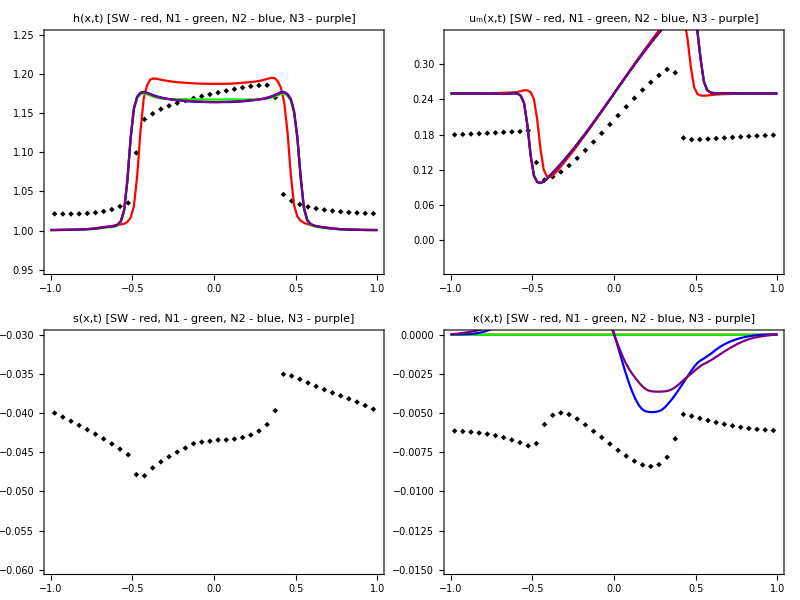

```mathematica
DataSet=Friction†R0p1†χ0p1†L;

Grid[{{Show[
ListPlot[{DataSet⟦All,{1,2}⟧},Joined->False,Frame->True,ImageSize->iSize,PlotStyle->{Black,Red,Black},PlotMarkers->{{markers⟦3⟧,Small},{markers⟦1⟧,Medium},{markers⟦3⟧,Medium}},PlotRange->{{-1,1},{0.95,1.25}}],
Plot[{hN0[x],hN1[x],hN2[x],hN3[x]},{x,-1,1},PlotStyle->color],PlotLabel->"h(x,t)   [SW - red, N1 - green, N2 - blue, N3 - purple]"],

Show[
ListPlot[{DataSet⟦All,{1,3}⟧},Joined->False,Frame->True,ImageSize->iSize,PlotStyle->{Black,Red,Black},PlotMarkers->{{markers⟦3⟧,Small},{markers⟦1⟧,Medium},{markers⟦3⟧,Medium}},PlotRange->{{-1,1},{-0.05,0.35}}],
Plot[{umN0[x],umN1[x],umN2[x],umN3[x]},{x,-1,1},PlotStyle->color],PlotLabel->"u_m(x,t)   [SW - red, N1 - green, N2 - blue, N3 - purple]"]},{

Show[
ListPlot[{DataSet⟦All,{1,4}⟧},Joined->False,Frame->True,ImageSize->iSize,PlotStyle->{Black,Red,Black},PlotMarkers->{{markers⟦3⟧,Small},{markers⟦1⟧,Medium},{markers⟦3⟧,Medium}},PlotRange->{{-1,1},{-0.06,-0.03}}],
Plot[{0,sN1[x]/3,sN2[x]/3,sN3[x]/3},{x,-1,1},PlotStyle->color],PlotLabel->"s(x,t)   [SW - red, N1 - green, N2 - blue, N3 - purple]"],

Show[
ListPlot[{DataSet⟦All,{1,5}⟧},Joined->False,Frame->True,ImageSize->iSize,PlotStyle->{Black,Red,Black},PlotMarkers->{{markers⟦3⟧,Medium},{markers⟦1⟧,Medium},{markers⟦3⟧,Medium}},PlotRange->{{-1,1},{-0.0,-0.015}}],
Plot[{0,0,κN2[x]/5,κN3[x]/5},{x,-1,1},PlotStyle->color,PlotRange->{{-1,1},All}],PlotLabel->"κ(x,t)   [SW - red, N1 - green, N2 - blue, N3 - purple]"]}}]
```

## Initial Data

```mathematica
UrawInitial = {{1.000894108651823,1.0008947974825393,1.0008960339768485,1.0008976506372627,1.0008995625420634,1.0009015596578406,1.0009035840669953,1.0009057750322465,1.0009084649967877,1.000911984380833,1.0009163844521702,1.0009216314593559,1.000927727632445,1.000934713031949,1.0009425741857028,1.0009512010711297,1.0009602796735853,1.0009696112388622,1.0009789798934372,1.000988618143764,1.0009978376689455,1.0010067220547179,1.0010155846887487,1.0010247962822358,1.0010346894795177,1.0010455567698089,1.0010575842016944,1.00107084523813,1.0010853132312239,1.0011008785016813,1.001117370755632,1.0011345918610108,1.001152359133295,1.0011705457145816,1.001189104970489,1.001208073604364,1.0012275573660847,1.0012477085827816,1.001268704934132,1.001290734923562,1.0013139898017704,1.0013386570391098,1.0013649087194183,1.0013928811543857,1.0014226480305128,1.0014541948271591,1.0014873850534938,1.0015220061051282,1.0015577681250323,1.001594347289114,1.0016315323520475,1.0016692094024489,1.0017074297704969,1.0017464208532656,1.00178654430114,1.0018282343742413,1.0018719264779499,1.001917993540018,1.0019667059391324,1.0020182214355626,1.002072602121465,1.002129847990536,1.0021899335321278,1.002252835286681,1.0023185434994888,1.0023870577932246,1.0024583728458398,1.0025324636054243,1.0026092797117632,1.0026887556524662,1.0027708377521451,1.002855522957164,1.0029428993549883,1.0030331761300184,1.0031266922119326,1.0032238981420363,1.0033253071646997,1.003431431219787,1.0035428399604256,1.0036598035974416,1.003782610361243,1.0039116426223134,1.004046694905634,1.0041882482398488,1.004336127085393,1.004490622920746,1.0046518264089863,1.004820016214362,1.004995265674634,1.005177678675624,1.0053674058157611,1.005564642447672,1.00576967255198,1.0059829293528475,1.006205181670603,1.0064374282694006,1.0066807694116444,1.006936372237731,1.0072052447354793,1.0074884566800184,1.0077867842277652,1.0081004906568487,1.0084297992254023,1.0087748378022923,1.0091356720082991,1.0095126415845455,1.0099066842697062,1.0103202097397217,1.0107576278097057,1.011224485357649,1.0117244233555214,1.0122538500627754,1.0127974988257524,1.0133325938559739,1.0138508964044393,1.014401997903715,1.01517965554964,1.0167532401893737,1.020925669972324,1.0338360342030295,1.070245271290998,1.1225377207380967,1.1536682016978268,1.1707764773412757,1.17344105248484,1.1742051665052686,1.1754681890531768,1.1765097730763718,1.1762544091903373,1.1756250704864808,1.1751421227305934,1.1752674631975084,1.1753760224483982,1.1751727805651924,1.174744043029758,1.1745135453662152,1.1744841700608848,1.1744389708822651,1.1742134500056443,1.17391392928107,1.1737031184282651,1.1735857553417963,1.1734379335323621,1.1732168732054933,1.1729800175403609,1.1727828021055957,1.1726063935598936,1.172411374609468,1.1722018938355827,1.172009207762859,1.1718415190662963,1.1716760797242374,1.1714948385332666,1.1713066621781791,1.171131398678805,1.1709746883257448,1.1708255328627684,1.170672235695748,1.1705130045497347,1.1703525947731503,1.1701954819853444,1.1700445942107747,1.1699027136331117,1.1697711532487478,1.1696474259992906,1.169526721380789,1.1694066070544227,1.1692894501838886,1.1691797738440641,1.1690798471347106,1.1689881427288609,1.1689011963294325,1.168815967128688,1.16873069213413,1.168644836955174,1.1685591847456651,1.1684757352624064,1.1683967118915326,1.1683231493346842,1.1682543230030888,1.1681885158692846,1.1681244209147121,1.1680621001431548,1.1680029473751947,1.1679488334368653,1.167901063629547,1.1678597313217987,1.167823586797879,1.1677904674472852,1.1677584181408527,1.167726995582792,1.167697535955067,1.1676720220406747,1.1676513597203932,1.167634256583614,1.1676175845180456,1.1675983508402532,1.1675751614994128,1.167548231728993,1.1675192892638724,1.1674911092676206,1.1674668082649127,1.1674477408961814,1.167432572452664,1.1674194620794245,1.1674067124704373,1.167393629749781,1.1673814470503876,1.1673713100700214,1.167363175795761,1.1673569771550254,1.1673527063878086,1.1673502002323204,1.1673496988810221,1.1673519531823642,1.1673575366332583,1.167366135538992,1.1673752592369455,1.1673804306123414,1.167380838254467,1.1673755805089636,1.16736371226822,1.167347909257685,1.1673311995507807,1.1673165334575417,1.1673070055780868,1.1673028287508536,1.167302473494988,1.1673042857368041,1.1673063260045433,1.1673067174889713,1.1673049599461387,1.1673018464932787,1.1672995253471508,1.1672991970901512,1.167302136130285,1.1673086089007578,1.1673172450579392,1.1673254877088322,1.1673305201460782,1.1673314724822057,1.1673297863091436,1.1673272237686538,1.1673223326685829,1.1673146785507613,1.1673072562379363,1.1673010393314276,1.167296361206207,1.167293097806086,1.1672911365487233,1.1672915668422061,1.167295194296734,1.1673019658343962,1.1673119475531133,1.1673257459368922,1.167343430903266,1.167364001773865,1.1673845492878816,1.167398585665941,1.1674021962611647,1.167394702231651,1.1673772917296437,1.1673525995870941,1.1673240207316193,1.1672955442868576,1.16727106110672,1.1672534542371849,1.1672440922421994,1.1672411233386635,1.167241511108035,1.16724265370848,1.1672422313887783,1.1672388212353864,1.1672324047441627,1.16722532379922,1.1672206821671405,1.1672195626020674,1.1672208662592278,1.16722445630046,1.167229138781328,1.1672315955103525,1.1672302290249792,1.167223102167804,1.1672101773561543,1.1671933887721226,1.1671748086149947,1.1671572035311013,1.167142805554795,1.1671326190063818,1.1671263477087612,1.1671229564150791,1.1671213773986246,1.1671211563756145,1.1671227822894763,1.1671266936821065,1.1671330290213489,1.167142412806265,1.1671535497419332,1.1671657114383918,1.167178056454252,1.1671892182842694,1.1671979671675845,1.167202966021657,1.1672041688110455,1.1672028425599152,1.1672019485580618,1.1672041717210397,1.167209944464509,1.1672211467658071,1.1672386053915398,1.1672615478888517,1.1672903764242375,1.1673247533791815,1.167363582601799,1.1674053260462542,1.1674488703248374,1.1674939965146574,1.1675412532861043,1.1675913462492515,1.1676446190865635,1.167700701463163,1.1677585935555248,1.16781738852153,1.1678771177201028,1.1679388314315036,1.1680037072208032,1.1680721291386686,1.1681438395718842,1.1682192464280539,1.168300664310751,1.1683919665955271,1.168496403315699,1.1686141164054273,1.1687414606509998,1.1688729214356566,1.1690042626342136,1.1691344757060944,1.1692651435778216,1.169398072596009,1.1695334370950223,1.1696699862814506,1.169806824991763,1.1699448567770738,1.1700864699364308,1.1702338891629567,1.1703879577862875,1.1705486125708733,1.170716445390648,1.1708933898124874,1.171081202942552,1.1712786472022252,1.171480076290485,1.1716775575592753,1.1718657564602033,1.1720459474983087,1.1722254792802755,1.172412279251446,1.1726084669010146,1.1728084558341756,1.1730035285203646,1.1731890905900495,1.1733667122039744,1.1735406090402294,1.1737146795951219,1.1738889776391117,1.1740586380158111,1.1742177217179992,1.174366932805768,1.1745155020890414,1.1746784618426744,1.174859367725206,1.1751004399664966,1.175390020573477,1.1756182421392312,1.1754518972378953,1.1743114524268636,1.1691400335355113,1.1582100966971858,1.1312992328020155,1.0876148335728701,1.0422018066610739,1.0229013216908278,1.0171574795521012,1.0151967196231906,1.0142927914740836,1.0136975209392416,1.0131860902022993,1.012671926941754,1.012144713555024,1.0116250709656835,1.0111306974764824,1.0106674360886165,1.01023280372523,1.0098219189428288,1.00943085262587,1.0090573506751466,1.0087002925083053,1.008359028219233,1.0080330170665994,1.0077217358107395,1.007424692321703,1.0071414292841447,1.0068714891775679,1.0066143618741772,1.0063694434296866,1.006136022745337,1.0059133007854628,1.0057004374743859,1.0054966138994372,1.0053010948338847,1.0051132783782886,1.0049327222855375,1.004759140986654,1.0045923760475792,1.00443235178937,1.0042790288366161,1.004132361591021,1.0039922613299685,1.0038585694774307,1.0037310472951175,1.0036093823319352,1.0034932052686893,1.003382111359522,1.0032756844502413,1.0031735215621176,1.0030752546484392,1.002980567793441,1.0028892101427727,1.0028010038058455,1.0027158443215238,1.00263369251626,1.00255455958616,1.0024784883582438,1.0024055321707566,1.0023357320008612,1.0022690946213797,1.0022055767202762,1.002145078051902,1.0020874424559565,1.002032464903797,1.0019799058404688,1.001929513198427,1.0018810462416572,1.001834293853735,1.0017890862037868,1.0017453026236203,1.0017028750148498,1.0016617834981392,1.0016220443604964,1.0015836945408532,1.0015467775520304,1.0015113334499008,1.0014773923556364,1.001444969795404,1.00141406350732,1.0013846526072503,1.001356698679836,1.0013301466401807,1.001304923873077,1.0012809384964125,1.001258079179196,1.0012362188648605,1.001215224522313,1.0011949730591234,1.00117536922005,1.00115635932351,1.001137937713998,1.0011201462706283,1.0011030653379718,1.0010867940576635,1.001071424799673,1.0010570197339401,1.0010435957545627,1.001031120460799,1.0010195176384284,1.001008678723936,1.0009984785412342,1.0009887950628586,1.0009795305653242,1.0009706262624514,1.0009620633654288,1.000953861548978,1.000946073009636,1.000938776044917,1.0009320603306904,1.0009260028874185,1.0009206597381328,1.000916050936954,1.0009121465311426,1.000908881532022,1.0009061720078531,1.0009039111366298,1.0009019614274637,1.0009002013075843,1.000898567701944,1.0008970833598612,1.0008958107879893,1.000894726385729,1.0008939845801934,1.0008938172704163},{0.25021512101764376,0.2502145992398692,0.25021430539284134,0.25021419097218306,0.25021427323012957,0.2502144307636276,0.250214563617852,0.2502146008715249,0.25021453847060304,0.25021438440260374,0.25021404019527405,0.2502134424743335,0.2502125480490809,0.2502113829074887,0.2502101239475275,0.25020883439709896,0.2502076255098882,0.25020664179671837,0.2502060452752549,0.2502059962993096,0.25020629450510656,0.25020699120358647,0.25020812427738737,0.2502095780927567,0.25021114754651075,0.2502126509578818,0.25021393893126487,0.25021492295660486,0.2502155959111122,0.2502160349794663,0.2502163815131966,0.2502168030891955,0.25021745445787275,0.25021844714606356,0.2502198332737104,0.2502216041979549,0.250223700626254,0.25022602829159124,0.2502284731696959,0.2502309125164851,0.25023322174952844,0.25023528057385314,0.25023698313142895,0.2502382546456004,0.2502390735725232,0.2502394902494171,0.2502396456111229,0.2502397606488585,0.2502401020323806,0.2502409286284736,0.25024248918445635,0.2502448953738131,0.2502481327121549,0.2502520618026187,0.2502564378898444,0.2502609614771435,0.2502653372552352,0.2502693248123413,0.2502727703034667,0.2502756138531682,0.2502778751601884,0.2502796257479656,0.2502809588858397,0.2502819669448024,0.2502827317354007,0.2502833279010831,0.2502838345650016,0.2502843475883596,0.2502849846827364,0.2502858781112098,0.2502871540201662,0.25028890231550566,0.25029114499750105,0.2502938126727246,0.2502967377679483,0.2502996688152903,0.2503023091162783,0.2503043652518029,0.25030552168124826,0.2503056443000238,0.2503046293487001,0.25030239120105824,0.25029907940083257,0.25029481632317907,0.25028925228788174,0.250282731976342,0.25027523597222306,0.2502667547039407,0.25025730923982503,0.2502468967285013,0.2502355962015959,0.2502234790921879,0.2502105265685973,0.25019644396220597,0.2501808518577533,0.2501632405434313,0.2501429010701834,0.2501192450769246,0.2500912850382981,0.250058515405739,0.2500209229106448,0.24997812621760856,0.24993014711616118,0.24987712263782455,0.2498191225354336,0.2497561942660042,0.24968773110813008,0.24961201078039058,0.24952584218054946,0.24942506801091913,0.24930700882176526,0.24917470959685445,0.24904048502045367,0.24892274709754625,0.24882813595133152,0.2487106156657991,0.24839795793874214,0.24749393557756844,0.24450877302372848,0.23436630610698592,0.20357989248020103,0.15723747001256955,0.12152017941987618,0.11501393861230882,0.1069650874733857,0.10413157403317738,0.10563545030347551,0.107126442008951,0.10758174523266925,0.10755140819695307,0.10814580588897532,0.10937086349747502,0.11048020682845501,0.11130492173495257,0.11181760630418441,0.11260657503816413,0.11367225032694622,0.11474309525852375,0.1156417444299826,0.11648519595981474,0.11747530889882463,0.11860053521036984,0.11971117222465351,0.120751117574362,0.12178701917806331,0.12288417277674032,0.12401855652567781,0.1251415544753437,0.12625807452570925,0.1274065740627761,0.12859817037759136,0.1298061926330385,0.13100875002195728,0.1322158200295997,0.13345061954468124,0.1347195748315999,0.13600932719454498,0.13730559106275478,0.13860556417640346,0.1399138075078792,0.14123434174765934,0.14256958048763319,0.14392216496644972,0.14529308357996318,0.1466785406038952,0.14807180216395482,0.14946921257047469,0.15087328327901006,0.15228936061538312,0.15372020819194024,0.15516439769340407,0.15661896630083277,0.15808237108545975,0.159555045200167,0.16103849335578974,0.16253476109337286,0.1640462002588941,0.16557432007394257,0.16711793798208435,0.1686726594483344,0.17023288459693325,0.17179487900443613,0.17335846010141137,0.17492648819809153,0.17650308756706998,0.178091726623238,0.17969374821663836,0.18130765429505016,0.18292961740679953,0.18455545364519146,0.18618298853012122,0.18781296899086475,0.18944813331518315,0.19109132656625796,0.19274415121617275,0.19440684596269384,0.19607886791086893,0.19775938749045968,0.1994479259002388,0.20114552736704275,0.20285369017097107,0.20457157355197608,0.2062959979691711,0.2080231943826586,0.2097502798747015,0.21147608471394735,0.21320186608872238,0.21493187034464717,0.21666994432208903,0.2184164568848927,0.22017021425989725,0.22192916577754362,0.22369007616056621,0.2254530482683712,0.22721517662580473,0.2289777910130566,0.2307445177377795,0.23251806773433153,0.23430100233663553,0.23608950540517512,0.23788261872823188,0.23968193193950593,0.24148359400131925,0.24328819426048687,0.24509631771780727,0.24690692322020225,0.2487201184552279,0.25053734014076046,0.25235367029563804,0.25417083517518846,0.2559874617180393,0.25780508099734306,0.25962343853795977,0.2614417724566721,0.263262129986243,0.265080887490884,0.26689836809977036,0.2687159767523652,0.270535441106288,0.2723597129258722,0.2741905154229352,0.27602740689291166,0.2778693020016635,0.27971619202649883,0.2815662161812472,0.28341492772534405,0.28525965309140966,0.28710015636587055,0.28893751475783164,0.29077268639581355,0.29261025260746043,0.2944479756038532,0.2962891917904211,0.29813237112039676,0.29997487947124063,0.3018144300478587,0.3036495208808472,0.3054798514727889,0.3073072268521949,0.309124038815672,0.3109433422817438,0.3127656398676597,0.31459020882586425,0.3164176958937652,0.31824759447590556,0.3200788422612696,0.3219097733143407,0.3237383252128262,0.32556491575928714,0.3273895792320104,0.32921058834778905,0.33102836787993817,0.33284328251049433,0.33465329387323084,0.33645720839813487,0.3382540567569211,0.34004460654868074,0.3418326059867783,0.34361695631753275,0.34540090691668324,0.3471863263934222,0.34897040420363973,0.3507576900721939,0.3525442967935395,0.3543276486848793,0.3561058877180302,0.3578779762570332,0.35964372188041677,0.3614037446948467,0.3631591196562358,0.3649108235071342,0.3666591955480058,0.3684036007219685,0.37014243475977726,0.37187474231891066,0.37359827482372354,0.3753153737564566,0.37702561544601143,0.3787305896481195,0.3804320943750734,0.3821308985218467,0.3838277464544853,0.38552382873752417,0.38721447516222113,0.38890332505110026,0.3905855105381896,0.39226000707681175,0.39392709431365897,0.3955867781845558,0.39724028734502703,0.39888751892282454,0.40052810005536915,0.4021602521857925,0.40378250670141574,0.4053941218615955,0.4069951950557949,0.4085866292918352,0.4101702913028367,0.4117487810955241,0.4133248463834808,0.4149005621748405,0.41647653333925705,0.4180512274725488,0.4196208786752275,0.4211805556922016,0.4227261380669478,0.42425607867468496,0.42577173399591195,0.42727602391223135,0.42877145356471913,0.43025895819936566,0.4317382508193463,0.4332089900422773,0.4346714408952292,0.43612597118318863,0.43757202750983826,0.43900788323133744,0.4404317375147625,0.4418433335458074,0.4432445563634534,0.44463822919001456,0.44602592003769054,0.4474065284741805,0.44877682650969875,0.4501334764588937,0.45147482448985954,0.45280106848460494,0.4541129220278145,0.4554102318507809,0.4566919184616782,0.45795716577840084,0.45920637251090474,0.4604405149921377,0.4616593227095833,0.4628603103892073,0.4640403660093056,0.4651990495087078,0.4663407229243557,0.4674726360085768,0.46859923628471994,0.46971829315331715,0.47082100125850873,0.4718975762403078,0.47294280443754455,0.47395522437271265,0.47493197289999983,0.47586887855111104,0.47675505130316936,0.47760141685127516,0.47844047054350913,0.479321080960911,0.4803089055876209,0.481425182861667,0.4822861710975726,0.4826221138960446,0.4813673035413474,0.4738771819836928,0.45787342540685494,0.4184792387717372,0.355924080168429,0.29384580727804155,0.26855424768182706,0.26141518901087624,0.2592162430105772,0.25834972739374196,0.25790069937704674,0.2575558590569566,0.2571975318755414,0.2568127122242787,0.2564284154860671,0.25606772028285685,0.2557383471372683,0.255437274164766,0.25515839846400507,0.2548968535799246,0.2546499348796951,0.2544164002528186,0.2541956196176218,0.25398710984275236,0.2537904097289887,0.25360509029138206,0.25343076143663046,0.2532670349948443,0.25311346085509545,0.2529694696693108,0.2528343490889809,0.25270726417139555,0.2525873163508733,0.2524736244062572,0.25236540595237766,0.2522620398444967,0.2521630979366773,0.2520683442067543,0.25197770561576494,0.2518912224270259,0.251808988497099,0.2517310934766801,0.2516575760331916,0.2515883914263427,0.2515233939581567,0.25146233615740726,0.2514048852976969,0.25135065164627085,0.2512992197388361,0.2512501786712435,0.2512031523087266,0.2511578282368919,0.25111397977255595,0.2510714758950034,0.25103027870195993,0.25099043125546966,0.25095203830621227,0.2509152409667848,0.25088018694172376,0.25084700021314177,0.2508157553814283,0.2507864606925541,0.2507590516996538,0.2507333957611222,0.25070930554557963,0.2506865580296369,0.25066491586481426,0.25064414957658876,0.2506240585573675,0.25060448676822145,0.250585330530505,0.2505665401729946,0.25054811808704736,0.25053011269829495,0.25051260711485723,0.25049570385620085,0.2504795090111187,0.25046411856932,0.2504496078373283,0.2504360236753119,0.2504233797722474,0.2504116558435514,0.25040080080703114,0.25039073779700183,0.2503813683123969,0.2503725760737727,0.2503642338989694,0.2503562151405147,0.25034840698745575,0.2503407222840918,0.2503331095152471,0.25032555978050663,0.25031810740481103,0.25031082313057923,0.2503038006999541,0.25029713848981666,0.25029092070762643,0.250285203705943,0.25028000873587847,0.250275320196493,0.25027109001596376,0.25026724773361686,0.2502637116890275,0.2502603990528615,0.2502572365560456,0.25025416905770703,0.2502511698625125,0.25024823501397475,0.25024537309798245,0.25024261159612154,0.2502399948015166,0.2502375605231412,0.2502353174153535,0.25023325008577324,0.2502313313418954,0.25022951720530834,0.25022775249453344,0.25022599460597394,0.2502242362346313,0.2502224888993774,0.2502208065414404,0.2502192574100727,0.25021779421921914,0.25021643482788175,0.25021575413166075},{-0.08340418076511646,-0.08340426360740488,-0.08340441059316996,-0.08340470196770272,-0.08340532898399658,-0.08340650438993451,-0.0834082249449574,-0.08341019229649917,-0.08341190982075067,-0.08341297904647764,-0.08341350509559803,-0.08341377958314747,-0.08341391086215039,-0.08341393222470231,-0.0834137843707555,-0.08341344362708741,-0.08341323068423079,-0.08341315898052729,-0.08341312385997524,-0.08341323722475556,-0.08341364454947628,-0.0834145625573812,-0.08341591489818072,-0.0834173483855128,-0.08341863564910504,-0.08341972632814613,-0.08342070683192918,-0.08342170356198689,-0.08342280305385665,-0.08342403077743818,-0.08342537145248892,-0.08342679566303593,-0.08342827543623951,-0.08342978938902573,-0.08343132398931148,-0.08343287451803993,-0.08343444574699468,-0.08343605148576923,-0.08343771299424413,-0.0834394569145163,-0.08344131317283224,-0.08344331266519031,-0.08344548411513296,-0.08344784977243709,-0.08345042047818026,-0.08345319136906465,-0.08345613646273717,-0.08345921662613433,-0.08346237986968734,-0.08346556846060285,-0.08346874347600808,-0.08347188225502909,-0.08347498927198224,-0.08347809795665118,-0.08348126361020532,-0.08348455312816075,-0.08348803317829617,-0.08349175969773183,-0.08349577129680873,-0.0835000876177422,-0.08350471214716908,-0.08350963776490848,-0.08351485278873028,-0.0835203455287204,-0.08352610622164021,-0.0835321263330401,-0.083538396214315,-0.08354490268590399,-0.08355162813986962,-0.08355855223571489,-0.08356565636643509,-0.08357293005897022,-0.08358037764528253,-0.08358802317307668,-0.08359591178289218,-0.0836041066451752,-0.08361268090663139,-0.08362170691429696,-0.08363126546525315,-0.0836413890345684,-0.08365210961366977,-0.08366347526625267,-0.08367543731720811,-0.08368805782367364,-0.08370128832733137,-0.0837151598916808,-0.08372966692230015,-0.08374483412728637,-0.08376065401321785,-0.08377712014867907,-0.08379423460438423,-0.0838120071214417,-0.08383046153636793,-0.08384964324066745,-0.0838696530905216,-0.08389063045042745,-0.08391272848274234,-0.08393611424883969,-0.08396092032617994,-0.0839872913109435,-0.08401532987713217,-0.08404504398967615,-0.08407643728512902,-0.08410949876271914,-0.08414420543087153,-0.08418058255903066,-0.08421875381517321,-0.08425908494557927,-0.08430226562257706,-0.08434915830910104,-0.0844002934163904,-0.08445500247296923,-0.0845107201409561,-0.08456369098215213,-0.08461278060798977,-0.08466785836182543,-0.08476121131652084,-0.0849779680463364,-0.08561202756353807,-0.0876745468586925,-0.0937814001336311,-0.10295286292499486,-0.10854244672872024,-0.11165225763799012,-0.11207331422051559,-0.11208714049336192,-0.11221976346726809,-0.1123541386946749,-0.11222265422645668,-0.11196767840856142,-0.1117711958777658,-0.11170404491870249,-0.11160290314946422,-0.11142847687867635,-0.11122613577748822,-0.1110528676064366,-0.11091039104853356,-0.11075293806564682,-0.11056015099307237,-0.11034984251020269,-0.11014971180072952,-0.1099615876403561,-0.10976260975060378,-0.1095442180238166,-0.10931756658205105,-0.10909287753344182,-0.10886603550342318,-0.10862915722150016,-0.10838336623028437,-0.10813613644508391,-0.10789123469114718,-0.10764551397625749,-0.10739438121759624,-0.10713637776892743,-0.10687180477326907,-0.10659963932370363,-0.1063177474075534,-0.10602535949303732,-0.10572404314459373,-0.10541640720440444,-0.10510472979814842,-0.10479082050980934,-0.10447618130655179,-0.1041614609534038,-0.10384582950910622,-0.1035274095891191,-0.1032046043816771,-0.10287703952693694,-0.10254534386300404,-0.10221027669467414,-0.10187215424418387,-0.10153088233214042,-0.10118623113984027,-0.10083803616251782,-0.1004863761623605,-0.1001317714911148,-0.09977518795680163,-0.09941769608104059,-0.09906001958885113,-0.09870235865142897,-0.09834457768358545,-0.0979865283646622,-0.09762827145967154,-0.09727011330146026,-0.09691247011934087,-0.09655567915849987,-0.0961999319635249,-0.09584534582359802,-0.0954920576712433,-0.09514031608758877,-0.09479059043320752,-0.09444355877248597,-0.09409988552707785,-0.09375994079249694,-0.09342367577928755,-0.09309070454856566,-0.09276058437826457,-0.09243306315407654,-0.09210820178116166,-0.09178640979051333,-0.09146813966688613,-0.09115375910852368,-0.09084353596940092,-0.09053748306240751,-0.09023550755263116,-0.08993757113341692,-0.08964406959312557,-0.08935595620573132,-0.08907403426010926,-0.08879869509458041,-0.08853026980068007,-0.0882688444010592,-0.08801395374865167,-0.08776519129523908,-0.08752220503210115,-0.08728416586856877,-0.08705065655451188,-0.08682156882666198,-0.08659704285227801,-0.08637793025955219,-0.08616467288321114,-0.08595815246836763,-0.08575981068804722,-0.08557019692021278,-0.08538949477293031,-0.08521733538168545,-0.08505280880761261,-0.0848952236495033,-0.08474385235151716,-0.08459803656174927,-0.08445790713137723,-0.08432366955297227,-0.08419604995630046,-0.08407581064885655,-0.08396379035039009,-0.08386071986560942,-0.08376647137297952,-0.08368069029814618,-0.08360271383240149,-0.08353160685435376,-0.08346662768612007,-0.08340741821545877,-0.0833539016490963,-0.08330531349281207,-0.08326133625782321,-0.08322285903009882,-0.08319066084857155,-0.08316525747845512,-0.08314677190659445,-0.08313603525292619,-0.08313165125506064,-0.08313032468819112,-0.083129955709358,-0.08313045635288593,-0.08313282814335371,-0.08313875322018624,-0.08315111466727124,-0.0831762125805867,-0.08322613989722044,-0.08331023437494407,-0.08342157955091287,-0.08355328464318536,-0.08369686137427218,-0.08384407318443496,-0.08398894489232928,-0.08412846290357812,-0.08426277032677709,-0.08439449511579548,-0.08452760992769058,-0.08466649664774145,-0.0848146917263865,-0.08497415919263629,-0.08514559078103767,-0.08532856774746954,-0.08552193829284113,-0.08572445325781691,-0.08593469561125278,-0.08615169218040884,-0.0863752099243819,-0.08660483565646353,-0.08684058593787099,-0.08708209466585219,-0.08732896255662981,-0.08758188628884164,-0.08784082434434401,-0.08810560761510633,-0.08837625397550283,-0.08865273167508386,-0.08893484722217734,-0.08922233831366286,-0.0895150801532586,-0.08981324573449063,-0.09011736451932423,-0.09042820793811346,-0.09074637807430691,-0.09107200717710505,-0.09140447600452505,-0.09174257776212785,-0.09208449879298003,-0.09242855411933625,-0.0927735666563605,-0.09311935648854987,-0.09346693373484903,-0.0938175548847778,-0.09417286077573503,-0.09453524026013355,-0.094904730996101,-0.09527973138127667,-0.09565780148066888,-0.09603589776966023,-0.09641151070539629,-0.09678371826760826,-0.09715343853973568,-0.09752300492902904,-0.09789525657394675,-0.09827240063671208,-0.09865500784441338,-0.09904152751598058,-0.09942856358054139,-0.09981193803787652,-0.10018815679491552,-0.10055572227800244,-0.10091577599710508,-0.10127174043558773,-0.10162798308226269,-0.10198796703288401,-0.1023526946435984,-0.10272020122910672,-0.10308637612667067,-0.10344672318618317,-0.1037982097703026,-0.10414037023770248,-0.10447527351714575,-0.10480652131543837,-0.105137769823795,-0.10547127979879738,-0.10580689286341874,-0.10614177006464101,-0.10647114218804586,-0.10679003057959591,-0.10709539551727587,-0.10738774130460792,-0.10767123982536833,-0.10795207210543296,-0.10823563924517927,-0.1085239859995007,-0.10881474962593676,-0.10910217667921251,-0.10937969413319817,-0.10964280512424382,-0.10989107554011966,-0.11012852299767212,-0.11036230272296843,-0.11059994379928387,-0.11084580213971995,-0.11109810020839997,-0.11134839230811427,-0.11158465344567316,-0.1117970616980935,-0.11198340794736683,-0.11215109634194752,-0.11231443135917896,-0.1124882985430481,-0.11268052188881977,-0.11288655296015705,-0.1130914731312612,-0.11327819498739339,-0.1134361528294445,-0.11356664550881894,-0.11368374656359885,-0.11380858421998274,-0.11396294529536202,-0.114150399829189,-0.11432338721767389,-0.11441681869552445,-0.114303557317747,-0.11332921632231407,-0.11107171173301415,-0.10584785688613557,-0.0977317327458892,-0.08946488122662148,-0.0860339406896793,-0.08506154973392652,-0.08476481444395273,-0.08465040663763848,-0.0845886558106957,-0.08454186594306566,-0.08449299435890326,-0.08444018002564217,-0.08438728301581708,-0.08433738861776909,-0.08429147641119893,-0.08424912599435813,-0.08420953559770149,-0.08417208156710296,-0.08413643150850098,-0.084102446496786,-0.08407006673884727,-0.08403925018335784,-0.08400995691377161,-0.08398215080811297,-0.08395579914540192,-0.08393086564550839,-0.08390730079420898,-0.08388503441883516,-0.08386397342051014,-0.08384400548431989,-0.0838250078841932,-0.08380685915777619,-0.08378945096678675,-0.08377269778469586,-0.08375654253293957,-0.08374095702012817,-0.08372593750613187,-0.08371149727946058,-0.08369765839310056,-0.08368444364439623,-0.08367186920483184,-0.08365993878165191,-0.08364864048331892,-0.08363794662970399,-0.08362781566968219,-0.08361819538932597,-0.08360902709297602,-0.08360025038857982,-0.08359180797371951,-0.08358365000670628,-0.08357573785260651,-0.08356804679897109,-0.08356056714484486,-0.08355330333983144,-0.08354627139163325,-0.08353949504073963,-0.08353300108310407,-0.0835268141747057,-0.08352095182217344,-0.08351542060008003,-0.0835102142947452,-0.0835053139013922,-0.08350068916356823,-0.08349630173632787,-0.08349210985956199,-0.08348807340860948,-0.08348415792240382,-0.08348033724347961,-0.08347659513684609,-0.0834729258087515,-0.08346933286041619,-0.08346582675992248,-0.08346242165468556,-0.083459132489173,-0.08345597295791912,-0.08345295423308903,-0.0834500841677224,-0.08344736689194679,-0.08344480290484627,-0.08344238951877403,-0.08344012121652306,-0.08343798961275387,-0.08343598315113859,-0.08343408698544058,-0.08343228348405603,-0.08343055373193262,-0.08342888006171437,-0.08342724894951273,-0.0834256533003758,-0.08342409360081748,-0.08342257793695389,-0.08342112058201887,-0.08341973882148418,-0.08341844878410834,-0.08341726161900076,-0.08341618108584878,-0.08341520300524166,-0.08341431628315714,-0.08341350492636992,-0.08341275074315183,-0.08341203656594603,-0.08341134945355207,-0.08341068256434728,-0.0834100345062565,-0.08340940814928693,-0.08340880864537853,-0.08340824178948027,-0.08340771198941785,-0.08340721983734892,-0.0834067636415137,-0.08340634052590834,-0.08340594628958423,-0.08340557796946223,-0.08340523946442877,-0.08340495158511813,-0.08340474986550667,-0.08340463420730065,-0.08340455703455563,-0.08340447091338087,-0.08340436351503205,-0.08340424175514663,-0.08340414455032716,-0.08340412694511465}};
```

## Data with q3 = hs instead of q3 = 1/3 hs

```mathematica
Urawq3 = {{1.000894108651824,1.0008947974825404,1.0008960339768496,1.000897650637263,1.000899562542064,1.000901559657841,1.0009035840669958,1.0009057750322468,1.000908464996788,1.0009119843808323,1.000916384452169,1.000921631459354,1.0009277276324433,1.0009347130319473,1.0009425741857014,1.0009512010711288,1.0009602796735848,1.0009696112388622,1.0009789798934372,1.0009886181437644,1.0009978376689461,1.0010067220547185,1.0010155846887496,1.0010247962822365,1.0010346894795181,1.0010455567698089,1.001057584201694,1.0010708452381292,1.0010853132312232,1.0011008785016804,1.0011173707556316,1.0011345918610106,1.001152359133295,1.0011705457145825,1.0011891049704906,1.0012080736043654,1.0012275573660865,1.001247708582783,1.0012687049341333,1.0012907349235638,1.0013139898017718,1.0013386570391112,1.0013649087194196,1.0013928811543868,1.0014226480305137,1.0014541948271602,1.0014873850534944,1.0015220061051284,1.0015577681250325,1.0015943472891138,1.0016315323520475,1.0016692094024489,1.0017074297704978,1.0017464208532676,1.0017865443011438,1.0018282343742462,1.0018719264779552,1.001917993540024,1.001966705939137,1.0020182214355655,1.0020726021214659,1.0021298479905338,1.002189933532123,1.002252835286674,1.002318543499481,1.0023870577932175,1.0024583728458332,1.002532463605419,1.0026092797117598,1.0026887556524648,1.002770837752145,1.002855522957165,1.0029428993549891,1.0030331761300189,1.0031266922119326,1.003223898142036,1.0033253071646993,1.003431431219787,1.0035428399604265,1.0036598035974427,1.0037826103612444,1.0039116426223142,1.004046694905634,1.0041882482398488,1.0043361270853932,1.0044906229207462,1.004651826408987,1.0048200162143632,1.0049952656746366,1.005177678675628,1.0053674058157664,1.005564642447679,1.0057696725519873,1.0059829293528548,1.006205181670609,1.006437428269405,1.0066807694116473,1.006936372237732,1.0072052447354791,1.0074884566800164,1.0077867842277621,1.0081004906568451,1.0084297992253983,1.0087748378022883,1.0091356720082942,1.0095126415845395,1.009906684269699,1.0103202097397141,1.010757627809698,1.0112244853576429,1.0117244233555167,1.0122538500627722,1.0127974988257495,1.0133325938559699,1.0138508964044328,1.0144019979037058,1.015179655549628,1.016753240189359,1.0209256699723077,1.0338360342030168,1.070245271291002,1.1225377207381095,1.1536682016978328,1.1707764773412803,1.1734410524848435,1.1742051665052669,1.1754681890531715,1.1765097730763698,1.176254409190335,1.1756250704864781,1.1751421227305912,1.1752674631975055,1.1753760224483958,1.1751727805651904,1.1747440430297567,1.1745135453662146,1.174484170060885,1.174438970882266,1.174213450005646,1.1739139292810714,1.1737031184282654,1.1735857553417965,1.1734379335323624,1.1732168732054933,1.172980017540361,1.1727828021055962,1.1726063935598938,1.1724113746094684,1.1722018938355838,1.17200920776286,1.1718415190662972,1.1716760797242385,1.1714948385332673,1.1713066621781798,1.1711313986788054,1.1709746883257455,1.1708255328627686,1.170672235695748,1.170513004549734,1.17035259477315,1.1701954819853437,1.1700445942107742,1.1699027136331115,1.1697711532487474,1.16964742599929,1.1695267213807878,1.1694066070544216,1.1692894501838875,1.1691797738440628,1.16907984713471,1.16898814272886,1.1689011963294316,1.1688159671286873,1.1687306921341296,1.1686448369551736,1.1685591847456651,1.168475735262406,1.1683967118915328,1.1683231493346846,1.1682543230030888,1.1681885158692846,1.168124420914712,1.1680621001431548,1.1680029473751954,1.1679488334368662,1.1679010636295484,1.1678597313217995,1.1678235867978803,1.1677904674472865,1.167758418140854,1.1677269955827934,1.1676975359550679,1.1676720220406756,1.1676513597203937,1.167634256583614,1.1676175845180459,1.1675983508402543,1.167575161499414,1.1675482317289942,1.1675192892638737,1.1674911092676221,1.167466808264914,1.1674477408961816,1.1674325724526642,1.1674194620794247,1.167406712470438,1.1673936297497818,1.1673814470503883,1.1673713100700218,1.167363175795761,1.1673569771550252,1.1673527063878084,1.16735020023232,1.1673496988810212,1.1673519531823628,1.1673575366332565,1.167366135538989,1.1673752592369426,1.167380430612339,1.1673808382544653,1.167375580508963,1.1673637122682212,1.1673479092576868,1.167331199550783,1.1673165334575433,1.167307005578087,1.1673028287508522,1.1673024734949853,1.1673042857367995,1.1673063260045358,1.167306717488961,1.1673049599461267,1.167301846493265,1.1672995253471368,1.1672991970901379,1.1673021361302742,1.167308608900751,1.1673172450579368,1.1673254877088364,1.1673305201460895,1.1673314724822244,1.167329786309167,1.1673272237686834,1.1673223326686195,1.1673146785507993,1.1673072562379716,1.1673010393314598,1.167296361206235,1.1672930978061085,1.167291136548739,1.1672915668422164,1.1672951942967411,1.1673019658344028,1.1673119475531202,1.1673257459368978,1.1673434309032693,1.1673640017738647,1.1673845492878747,1.1673985856659244,1.167402196261143,1.1673947022316307,1.1673772917296277,1.1673525995870841,1.1673240207316145,1.167295544286856,1.1672710611067207,1.1672534542371866,1.1672440922422007,1.1672411233386644,1.1672415111080352,1.1672426537084801,1.1672422313887787,1.167238821235388,1.1672324047441638,1.1672253237992212,1.1672206821671414,1.1672195626020683,1.1672208662592285,1.1672244563004608,1.1672291387813294,1.1672315955103534,1.1672302290249803,1.1672231021678052,1.167210177356156,1.1671933887721246,1.1671748086149973,1.1671572035311035,1.167142805554797,1.1671326190063829,1.1671263477087617,1.167122956415079,1.1671213773986246,1.1671211563756148,1.1671227822894763,1.1671266936821063,1.167133029021349,1.1671424128062653,1.167153549741933,1.167165711438392,1.1671780564542518,1.1671892182842696,1.167197967167585,1.1672029660216576,1.1672041688110464,1.1672028425599168,1.1672019485580636,1.1672041717210413,1.1672099444645105,1.167221146765808,1.1672386053915407,1.167261547888852,1.1672903764242375,1.1673247533791815,1.1673635826017992,1.1674053260462545,1.1674488703248378,1.1674939965146582,1.167541253286104,1.1675913462492513,1.167644619086563,1.167700701463163,1.1677585935555248,1.1678173885215306,1.1678771177201042,1.1679388314315058,1.1680037072208056,1.1680721291386709,1.1681438395718862,1.1682192464280554,1.1683006643107527,1.1683919665955287,1.1684964033157001,1.1686141164054282,1.1687414606510007,1.1688729214356568,1.169004262634214,1.1691344757060949,1.1692651435778223,1.1693980725960096,1.1695334370950237,1.1696699862814524,1.1698068249917646,1.1699448567770752,1.170086469936432,1.1702338891629573,1.170387957786287,1.1705486125708722,1.170716445390647,1.1708933898124858,1.1710812029425504,1.1712786472022239,1.1714800762904831,1.1716775575592737,1.1718657564602022,1.1720459474983083,1.172225479280275,1.172412279251446,1.1726084669010153,1.1728084558341765,1.173003528520366,1.1731890905900504,1.173366712203975,1.1735406090402294,1.173714679595121,1.1738889776391104,1.1740586380158091,1.1742177217179965,1.1743669328057647,1.1745155020890388,1.1746784618426722,1.1748593677252042,1.175100439966494,1.1753900205734724,1.1756182421392274,1.1754518972378916,1.174311452426863,1.169140033535505,1.1582100966971778,1.1312992328019966,1.087614833572851,1.0422018066610574,1.022901321690825,1.0171574795521015,1.0151967196231908,1.0142927914740838,1.013697520939242,1.0131860902022995,1.0126719269417546,1.012144713555025,1.0116250709656842,1.0111306974764833,1.0106674360886174,1.0102328037252306,1.009821918942829,1.0094308526258706,1.0090573506751472,1.0087002925083062,1.0083590282192338,1.0080330170666003,1.0077217358107409,1.0074246923217043,1.007141429284146,1.006871489177569,1.006614361874178,1.0063694434296875,1.0061360227453378,1.0059133007854628,1.0057004374743856,1.005496613899437,1.0053010948338845,1.0051132783782881,1.0049327222855369,1.0047591409866539,1.0045923760475788,1.00443235178937,1.0042790288366166,1.004132361591021,1.0039922613299679,1.00385856947743,1.0037310472951164,1.0036093823319343,1.0034932052686882,1.0033821113595207,1.00327568445024,1.003173521562116,1.0030752546484376,1.0029805677934402,1.0028892101427722,1.0028010038058452,1.002715844321524,1.0026336925162596,1.0025545595861596,1.0024784883582436,1.0024055321707561,1.002335732000861,1.0022690946213786,1.0022055767202753,1.002145078051901,1.0020874424559552,1.002032464903796,1.0019799058404681,1.001929513198427,1.001881046241657,1.001834293853735,1.0017890862037868,1.0017453026236203,1.00170287501485,1.0016617834981394,1.0016220443604968,1.0015836945408534,1.0015467775520306,1.0015113334499008,1.0014773923556364,1.001444969795403,1.0014140635073188,1.0013846526072485,1.001356698679834,1.001330146640179,1.001304923873076,1.0012809384964116,1.0012580791791952,1.0012362188648605,1.0012152245223134,1.0011949730591243,1.0011753692200513,1.0011563593235113,1.0011379377139986,1.0011201462706292,1.0011030653379716,1.001086794057663,1.0010714247996724,1.0010570197339392,1.0010435957545618,1.001031120460799,1.0010195176384287,1.0010086787239365,1.0009984785412342,1.0009887950628586,1.0009795305653246,1.000970626262452,1.0009620633654297,1.0009538615489784,1.0009460730096365,1.0009387760449173,1.0009320603306908,1.0009260028874185,1.000920659738133,1.0009160509369541,1.0009121465311426,1.0009088815320222,1.0009061720078534,1.0009039111366298,1.0009019614274641,1.0009002013075845,1.000898567701944,1.0008970833598616,1.0008958107879897,1.0008947263857297,1.0008939845801939,1.0008938172704172},{0.25021512101764287,0.2502145992398688,0.2502143053928415,0.2502141909721833,0.2502142732301302,0.25021443076362837,0.25021456361785277,0.2502146008715259,0.2502145384706042,0.250214384402605,0.25021404019527516,0.25021344247433447,0.2502125480490822,0.2502113829074903,0.2502101239475292,0.2502088343971004,0.2502076255098895,0.2502066417967198,0.25020604527525636,0.2502059962993106,0.2502062945051075,0.2502069912035871,0.2502081242773876,0.2502095780927565,0.2502111475465101,0.2502126509578815,0.2502139389312644,0.250214922956604,0.25021559591111087,0.2502160349794649,0.2502163815131952,0.2502168030891945,0.2502174544578719,0.25021844714606306,0.2502198332737105,0.25022160419795525,0.25022370062625476,0.250226028291592,0.25022847316969615,0.25023091251648544,0.2502332217495288,0.25023528057385297,0.2502369831314284,0.25023825464560023,0.2502390735725234,0.2502394902494175,0.2502396456111237,0.2502397606488598,0.2502401020323824,0.25024092862847525,0.2502424891844577,0.2502448953738139,0.2502481327121543,0.25025206180261644,0.25025643788984075,0.2502609614771387,0.25026533725523,0.25026932481233655,0.2502727703034622,0.250275613853165,0.2502778751601873,0.2502796257479669,0.2502809588858431,0.25028196694480753,0.25028273173540655,0.25028332790108837,0.25028383456500564,0.25028434758836166,0.25028498468273697,0.2502858781112093,0.25028715402016466,0.2502889023155037,0.25029114499749944,0.2502938126727233,0.2502967377679475,0.25029966881528987,0.25030230911627827,0.250304365251803,0.25030552168124837,0.2503056443000238,0.2503046293487001,0.2503023912010585,0.2502990794008329,0.2502948163231797,0.250289252287882,0.2502827319763418,0.25027523597222223,0.25026675470393916,0.2502573092398228,0.2502468967284983,0.2502355962015915,0.2502234790921825,0.2502105265685912,0.2501964439621999,0.2501808518577483,0.2501632405434274,0.25014290107018056,0.2501192450769226,0.25009128503829686,0.25005851540573865,0.2500209229106449,0.24997812621760918,0.24993014711616238,0.2498771226378263,0.24981912253543595,0.24975619426600726,0.2496877311081343,0.24961201078039613,0.249525842180555,0.24942506801092407,0.24930700882176954,0.24917470959685792,0.24904048502045667,0.24892274709755016,0.2488281359513371,0.24871061566580635,0.24839795793875127,0.24749393557757943,0.24450877302374052,0.23436630610699505,0.2035798924801973,0.15723747001255411,0.12152017941986375,0.11501393861230541,0.10696508747338576,0.10413157403317655,0.10563545030347307,0.10712644200895248,0.10758174523267255,0.10755140819695716,0.10814580588898132,0.10937086349747918,0.11048020682845835,0.11130492173495479,0.11181760630418547,0.11260657503816508,0.11367225032694694,0.11474309525852439,0.11564174442998329,0.11648519595981507,0.11747530889882393,0.11860053521036903,0.11971117222465259,0.1207511175743605,0.12178701917806165,0.12288417277673834,0.12401855652567532,0.12514155447534128,0.12625807452570706,0.12740657406277403,0.1285981703775898,0.12980619263303728,0.1310087500219566,0.13221582002959947,0.13345061954468085,0.1347195748315992,0.13600932719454403,0.13730559106275406,0.13860556417640318,0.13991380750787913,0.14123434174765923,0.14256958048763285,0.1439221649664493,0.1452930835799629,0.14667854060389465,0.14807180216395419,0.14946921257047424,0.15087328327900984,0.15228936061538237,0.15372020819193927,0.15516439769340262,0.1566189663008308,0.15808237108545797,0.15955504520016572,0.16103849335578915,0.16253476109337273,0.16404620025889388,0.16557432007394182,0.1671179379820832,0.1686726594483332,0.17023288459693214,0.1717948790044352,0.17335846010141054,0.17492648819809023,0.17650308756706817,0.17809172662323597,0.17969374821663614,0.1813076542950482,0.18292961740679764,0.18455545364518994,0.18618298853012027,0.18781296899086425,0.18944813331518282,0.19109132656625794,0.19274415121617317,0.19440684596269442,0.1960788679108693,0.19775938749045982,0.19944792590023896,0.2011455273670425,0.20285369017097032,0.20457157355197492,0.2062959979691702,0.20802319438265798,0.20975027987470102,0.2114760847139469,0.213201866088722,0.21493187034464678,0.21666994432208894,0.21841645688489286,0.2201702142598973,0.22192916577754343,0.22369007616056624,0.2254530482683704,0.22721517662580334,0.22897779101305504,0.23074451773777827,0.2325180677343303,0.2343010023366337,0.23608950540517384,0.2378826187282303,0.23968193193950446,0.24148359400131814,0.2432881942604865,0.24509631771780765,0.24690692322020344,0.24872011845522904,0.2505373401407592,0.25235367029563716,0.25417083517518735,0.2559874617180356,0.2578050809973401,0.25962343853795633,0.261441772456668,0.2632621299862409,0.265080887490882,0.26689836809976897,0.2687159767523649,0.2705354411062888,0.27235971292587313,0.27419051542293926,0.27602740689291855,0.27786930200166937,0.2797161920265041,0.281566216181255,0.28341492772535354,0.28525965309141904,0.2871001563658784,0.2889375147578392,0.29077268639581577,0.2926102526074672,0.2944479756038587,0.29628919179042523,0.29813237112039953,0.2999748794712427,0.30181443004785946,0.30364952088084796,0.30547985147278767,0.30730722685219025,0.3091240388156671,0.3109433422817409,0.31276563986765793,0.3145902088258644,0.3164176958937661,0.3182475944759077,0.3200788422612729,0.3219097733143445,0.3237383252128294,0.32556491575928936,0.32738957923201173,0.3292105883477899,0.3310283678799381,0.33284328251049483,0.33465329387323206,0.3364572083981363,0.33825405675692233,0.34004460654868146,0.341832605986779,0.34361695631753353,0.3454009069166843,0.34718632639342334,0.34897040420364067,0.35075769007219465,0.35254429679353977,0.35432764868487904,0.35610588771802965,0.35787797625703305,0.35964372188041693,0.3614037446948467,0.3631591196562354,0.36491082350713366,0.36665919554800563,0.3684036007219686,0.370142434759778,0.37187474231891204,0.37359827482372554,0.3753153737564594,0.37702561544601465,0.3787305896481229,0.3804320943750764,0.38213089852184934,0.38382774645448775,0.3855238287375262,0.38721447516222274,0.38890332505110153,0.3905855105381906,0.39226000707681297,0.3939270943136599,0.39558677818455695,0.3972402873450285,0.39888751892282603,0.40052810005537054,0.40216025218579426,0.4037825067014176,0.40539412186159773,0.40699519505579707,0.40858662929183753,0.4101702913028389,0.411748781095526,0.4133248463834823,0.4149005621748418,0.41647653333925805,0.41805122747254975,0.41962087867522874,0.4211805556922027,0.42272613806694875,0.42425607867468595,0.42577173399591306,0.4272760239122329,0.4287714535647207,0.4302589581993671,0.4317382508193476,0.43320899004227875,0.43467144089523047,0.43612597118318974,0.4375720275098394,0.43900788323133866,0.44043173751476383,0.4418433335458088,0.4432445563634542,0.4446382291900151,0.44602592003769126,0.4474065284741812,0.44877682650969986,0.45013347645889507,0.4514748244898613,0.4528010684846068,0.4541129220278162,0.45541023185078255,0.4566919184616796,0.4579571657784015,0.45920637251090474,0.46044051499213734,0.4616593227095827,0.4628603103892065,0.4640403660093054,0.4651990495087086,0.46634072292435713,0.46747263600857863,0.4685992362847221,0.469718293153319,0.47082100125851034,0.4718975762403088,0.47294280443754444,0.4739552243727115,0.47493197289999756,0.47586887855110743,0.47675505130316476,0.477601416851269,0.4784404705435013,0.4793210809609031,0.48030890558761363,0.48142518286166136,0.4822861710975687,0.48262211389603815,0.4813673035413422,0.4738771819836781,0.4578734254068396,0.4184792387717047,0.35592408016840005,0.29384580727801696,0.2685542476818218,0.26141518901087596,0.25921624301057805,0.2583497273937433,0.25790069937704796,0.25755585905695755,0.25719753187554206,0.25681271222427937,0.25642841548606793,0.25606772028285785,0.2557383471372694,0.2554372741647675,0.2551583984640069,0.2548968535799262,0.25464993487969645,0.25441640025281964,0.2541956196176227,0.2539871098427534,0.2537904097289894,0.25360509029138256,0.25343076143663085,0.2532670349948448,0.2531134608550954,0.2529694696693108,0.25283434908898106,0.2527072641713959,0.252587316350873,0.25247362440625676,0.252365405952377,0.2522620398444959,0.25216309793667613,0.25206834420675295,0.2519777056157637,0.25189122242702455,0.25180898849709826,0.2517310934766796,0.2516575760331914,0.2515883914263425,0.2515233939581564,0.25146233615740676,0.25140488529769617,0.25135065164627,0.25129921973883546,0.25125017867124283,0.251203152308726,0.25115782823689137,0.2511139797725553,0.2510714758950028,0.2510302787019599,0.2509904312554698,0.2509520383062124,0.25091524096678464,0.2508801869417237,0.2508470002131418,0.2508157553814284,0.2507864606925546,0.2507590516996542,0.2507333957611225,0.2507093055455798,0.250686558029637,0.2506649158648147,0.25064414957658876,0.25062405855736725,0.2506044867682212,0.25058533053050464,0.2505665401729945,0.25054811808704747,0.2505301126982951,0.2505126071148577,0.25049570385620135,0.2504795090111193,0.2504641185693204,0.2504496078373286,0.25043602367531215,0.25042337977224755,0.25041165584355113,0.2504008008070304,0.25039073779700105,0.25038136831239644,0.25037257607377217,0.25036423389896867,0.250356215140514,0.25034840698745475,0.2503407222840906,0.2503331095152461,0.2503255597805054,0.2503181074048099,0.25031082313057856,0.25030380069995384,0.2502971384898169,0.25029092070762643,0.2502852037059434,0.2502800087358788,0.25027532019649346,0.2502710900159643,0.2502672477336173,0.25026371168902795,0.2502603990528622,0.2502572365560459,0.2502541690577072,0.2502511698625128,0.25024823501397486,0.2502453730979822,0.2502426115961208,0.2502399948015156,0.2502375605231401,0.25023531741535204,0.25023325008577135,0.2502313313418935,0.2502295172053062,0.25022775249453155,0.2502259946059717,0.25022423623462897,0.2502224888993756,0.2502208065414387,0.2502192574100712,0.2502177942192178,0.25021643482788036,0.2502157541316599},{-0.2502125422953482,-0.25021279082221304,-0.2502132317795085,-0.2502141059031071,-0.25021598695198866,-0.2502195131698022,-0.25022467483487043,-0.25023057688949546,-0.25023572946224987,-0.25023893713943046,-0.2502405152867913,-0.25024133874943943,-0.2502417325864481,-0.25024179667410384,-0.2502413531122634,-0.25024033088125913,-0.2502396920526895,-0.25023947694157933,-0.25023937157992326,-0.25023971167426445,-0.250240933648427,-0.250243687672142,-0.2502477446945407,-0.25025204515653715,-0.25025590694731403,-0.2502591789844374,-0.2502621204957862,-0.2502651106859593,-0.25026840916156845,-0.25027209233231285,-0.250276114357465,-0.25028038698910615,-0.250284826308717,-0.2502893681670757,-0.2502939719679331,-0.25029862355411864,-0.2503033372409825,-0.2503081544573059,-0.2503131389827305,-0.2503183707435469,-0.2503239395184949,-0.2503299379955697,-0.2503364523453981,-0.2503435493173108,-0.25035126143454056,-0.2503595741071939,-0.2503684093882116,-0.25037764987840305,-0.25038713960906195,-0.25039670538180847,-0.2504062304280241,-0.2504156467650873,-0.2504249678159471,-0.25043429386995447,-0.25044379083061735,-0.2504536593844843,-0.2504640995348908,-0.25047527909319767,-0.2504873138904279,-0.25050026285322713,-0.25051413644150605,-0.25052891329472243,-0.2505445583661864,-0.2505610365861556,-0.25057831866491476,-0.25059637899911497,-0.2506151886429407,-0.2506347080577088,-0.25065488441960704,-0.2506756567071441,-0.25069696909930567,-0.25071879017691157,-0.2507411329358487,-0.25076406951923075,-0.2507877353486765,-0.2508123199355249,-0.250838042719893,-0.2508651207428896,-0.25089379639575843,-0.2509241671037046,-0.25095632884100916,-0.25099042579875824,-0.2510263119516244,-0.25106417347102095,-0.2511038649819941,-0.25114547967504264,-0.2511890007669009,-0.25123450238185996,-0.2512819620396551,-0.25133136044603976,-0.25138270381315597,-0.2514360213643288,-0.2514913846091077,-0.25154892972200626,-0.25160895927156834,-0.2516718913512855,-0.2517381854482296,-0.2518083427465213,-0.2518827609785418,-0.25196187393283187,-0.25204598963139735,-0.25213513196902904,-0.25222931185538744,-0.25232849628815734,-0.252432616292614,-0.25254174767709064,-0.25265626144551734,-0.2527772548367345,-0.2529067968677278,-0.25304747492730023,-0.253200880249169,-0.2533650074189062,-0.25353216042286686,-0.2536910729464544,-0.2538383418239662,-0.2540035750854718,-0.2542836339495569,-0.2549339041390022,-0.25683608269060587,-0.2630236405760701,-0.281344200400894,-0.3088585887749897,-0.3256273401861625,-0.33495677291397197,-0.3362199426615475,-0.3362614214800833,-0.33665929040179987,-0.337062416084022,-0.33666796267936766,-0.3359030352256812,-0.33531358763329444,-0.3351121347561045,-0.3348087094483898,-0.33428543063602684,-0.33367840733246257,-0.33315860281930754,-0.33273117314559836,-0.3322588141969382,-0.3316804529792151,-0.33104952753060624,-0.3304491354021865,-0.32988476292106605,-0.3292878292518092,-0.32863265407144815,-0.3279526997461526,-0.327278632600326,-0.32659810651027094,-0.3258874716645028,-0.3251500986908562,-0.3244084093352547,-0.3236737040734444,-0.3229365419287755,-0.3221831436527925,-0.3214091333067871,-0.3206154143198131,-0.3197989179711176,-0.31895324222266697,-0.31807607847911834,-0.31717212943378653,-0.31624922161321745,-0.3153141893944482,-0.3143724615294303,-0.31342854391965724,-0.31248438286021313,-0.3115374885273207,-0.31058222876735986,-0.30961381314503417,-0.3086311185808142,-0.30763603158901554,-0.3066308300840254,-0.3056164627325537,-0.3045926469964224,-0.30355869341952146,-0.3025141084875542,-0.3014591284870825,-0.3003953144733459,-0.29932556387040704,-0.2982530882431245,-0.2971800587665563,-0.29610707595428976,-0.2950337330507592,-0.29395958509398934,-0.29288481437901703,-0.29181033990438315,-0.290737410358025,-0.28966703747550215,-0.2885997958905773,-0.287536037470797,-0.28647617301373285,-0.2854209482627692,-0.2843717712996253,-0.2833306763174607,-0.2822996565812363,-0.2812798223774934,-0.28027102733786513,-0.2792721136456998,-0.2782817531347971,-0.27729918946223364,-0.27632460534348957,-0.2753592293715449,-0.27440441900066354,-0.2734612773255757,-0.27253060790820666,-0.2716124491872257,-0.2707065226578962,-0.26981271340025303,-0.26893220877937885,-0.2680678686171962,-0.2672221027803303,-0.2663960852837447,-0.2655908094020456,-0.26480653320318565,-0.2640418612459665,-0.263295573885733,-0.2625666150963236,-0.26185249760573015,-0.2611519696635623,-0.2604647064800141,-0.2597911285568616,-0.25913379077868126,-0.2584940186496535,-0.2578744574051166,-0.2572794320641484,-0.2567105907606394,-0.256168484318789,-0.25565200614505584,-0.2551584264228448,-0.25468567094853045,-0.2542315570545905,-0.25379410968530913,-0.2533737213942157,-0.25297100865902133,-0.25258814986902167,-0.2522274319466959,-0.25189137105129067,-0.25158215959693037,-0.2512994141190093,-0.25104207089446656,-0.25080814149718145,-0.2505948205629822,-0.25039988305822414,-0.25022225464618686,-0.25006170494705565,-0.24991594047817112,-0.24978400877318516,-0.24966857709001114,-0.24957198254544932,-0.2494957724351386,-0.2494403157196184,-0.24940810575866948,-0.2493949537651032,-0.2493909740645103,-0.24938986712801625,-0.24939136905860404,-0.2493984844300172,-0.24941625966053085,-0.2494533440018144,-0.24952863774181527,-0.24967841969179463,-0.24993070312500476,-0.25026473865290744,-0.25065985392969264,-0.2510905841229096,-0.25153221955335586,-0.25196683467700554,-0.2523853887107313,-0.25278831098031934,-0.2531834853473742,-0.2535828297830639,-0.2539994899432222,-0.2544440751791623,-0.2549224775779147,-0.25543677234311996,-0.2559857032424152,-0.2565658148785288,-0.25717335977345457,-0.25780408683376066,-0.2584550765412277,-0.25912562977314624,-0.2598145069693907,-0.2605217578136127,-0.26124628399755623,-0.26198688766988903,-0.2627456588665249,-0.26352247303303244,-0.26431682284531965,-0.26512876192650914,-0.2659581950252518,-0.2668045416665316,-0.2676670149409876,-0.2685452404597744,-0.2694397372034706,-0.2703520935579714,-0.27128462381433877,-0.2722391342229191,-0.27321602153131386,-0.2742134280135742,-0.27522773328638284,-0.2762534963789396,-0.2772856623580081,-0.27832069996908093,-0.2793580694656493,-0.2804008012045472,-0.2814526646543337,-0.2825185823272054,-0.2836057207804008,-0.28471419298830314,-0.2858391941438303,-0.2869734044420068,-0.2881076933089809,-0.2892345321161893,-0.2903511548028255,-0.29146031561920804,-0.29256901478708836,-0.29368576972184135,-0.29481720191013716,-0.2959650235332407,-0.29712458254794194,-0.2982856907416238,-0.29943581411362896,-0.3005644703847462,-0.30166716683400735,-0.30274732799131554,-0.30381522130676375,-0.3048839492467884,-0.30596390109865224,-0.3070580839307948,-0.3081606036873192,-0.3092591283800109,-0.31034016955854865,-0.31139462931090733,-0.3124211107131074,-0.313425820551438,-0.31441956394631654,-0.3154133094713867,-0.31641383939639384,-0.31742067859025785,-0.3184253101939246,-0.3194134265641394,-0.32037009173879005,-0.32128618655183017,-0.3221632239138262,-0.32301371947610724,-0.3238562163163007,-0.32470691773553884,-0.32557195799850225,-0.3264442488778099,-0.32730653003763693,-0.328139082399594,-0.3289284153727311,-0.3296732266203588,-0.3303855689930162,-0.3310869081689053,-0.33179983139785163,-0.3325374064191595,-0.33329430062519894,-0.33404517692434155,-0.3347539603370181,-0.33539118509427945,-0.3359502238421001,-0.3364532890258429,-0.33694329407753754,-0.3374648956291445,-0.3380415656664588,-0.33865965888047034,-0.3392744193937828,-0.3398345849621794,-0.34030845848833297,-0.340699936526457,-0.34105123969079676,-0.3414257526599482,-0.3418888358860852,-0.3424511994875642,-0.34297016165301836,-0.3432504560865705,-0.34291067195324165,-0.33998764896694467,-0.3332151351990462,-0.31754357065840155,-0.2931951982376597,-0.2683946436798577,-0.2581018220690387,-0.25518464920178197,-0.2542944433318608,-0.2539512199129178,-0.25376596743208923,-0.2536255978291992,-0.2534789830767119,-0.2533205400769286,-0.253161849047453,-0.25301216585330855,-0.2528744292335978,-0.25274737798307495,-0.2526286067931045,-0.25251624470130873,-0.25240929452550276,-0.25230733949035794,-0.2522102002165421,-0.25211775055007424,-0.252029870741316,-0.2519464524243401,-0.2518673974362068,-0.25179259693652634,-0.25172190238262804,-0.25165510325650636,-0.251591920261531,-0.25153201645296,-0.25147502365257973,-0.2514205774733286,-0.25136835290036,-0.25131809335408717,-0.2512696275988182,-0.25122287106038377,-0.2511778125183948,-0.25113449183838127,-0.25109297517930174,-0.25105333093318905,-0.2510156076144961,-0.2509798163449563,-0.2509459214499574,-0.2509138398891127,-0.25088344700904697,-0.25085458616797784,-0.25082708127892767,-0.25080075116573874,-0.2507754239211576,-0.250750950020118,-0.2507272135578185,-0.25070414039691213,-0.25068170143453344,-0.2506599100194932,-0.25063881417489864,-0.25061848512221757,-0.2505990032493107,-0.2505804425241153,-0.25056285546651796,-0.2505462618002374,-0.2505306428842332,-0.25051594170417496,-0.2505020674907039,-0.25048890520898326,-0.2504763295786857,-0.25046422022582837,-0.25045247376721136,-0.2504410117304388,-0.2504297854105383,-0.25041877742625474,-0.25040799858124896,-0.25039748027976794,-0.2503872649640573,-0.2503773974675194,-0.2503679188737577,-0.2503588626992673,-0.250350252503167,-0.25034210067583973,-0.2503344087145377,-0.2503271685563207,-0.25032036364956767,-0.2503139688382602,-0.2503079494534146,-0.2503022609563209,-0.2502968504521678,-0.2502916611957982,-0.2502866401851438,-0.2502817468485389,-0.2502769599011278,-0.25027228080245245,-0.2502677338108612,-0.2502633617460558,-0.2502592164644517,-0.25025534635232405,-0.25025178485700117,-0.25024854325754525,-0.25024560901572396,-0.2502429488494704,-0.2502405147791088,-0.25023825222945417,-0.2502361096978366,-0.2502340483606549,-0.2502320476930407,-0.25023010351876823,-0.25022822444785947,-0.2502264259361345,-0.2502247253684399,-0.25022313596825313,-0.25022165951204645,-0.2502202909245409,-0.25021902157772496,-0.2502178388687526,-0.2502167339083865,-0.2502157183932864,-0.25021485475535443,-0.2502142495965201,-0.250213902621902,-0.250213671103667,-0.25021341274014286,-0.2502130905450962,-0.25021272526543953,-0.25021243365098067,-0.250212380835343}};
```

```mathematica
Norm[(UrawInitial - Urawq3)[[1]]]
Norm[(UrawInitial - Urawq3)[[2]]]
```

1.23726×10^-13

7.89535×10^-14

## Forward Euler with Limiters

```mathematica
Urecons=Recon[Uraw,"Periodic"];

Uright=Urecons⟦All,;;-2,1⟧;
Uleft=Urecons⟦All,2;;,2⟧;
dU=Uright⟦All,2;;⟧-Uleft⟦All,;;-2⟧;
```

```mathematica
Uright[[All,1]]
```

{1.0004,0.250319,-0.250968}

```mathematica
Uleft[[All,1]]
```

{1.00038,0.250312,-0.251052}

```mathematica
Uraw[[All,1]]
```

{1.00038,0.250312,-0.251052}

```mathematica
TestU = {{U1im1, U1i, U1ip1},{U2im1, U2i, U2ip1},{U3im1, U3i, U3ip1}};
Residuum[TestU]
```

{{-1/dx,-1/dx,-(-0.475 (1/2 (1)+1/2 1) (U1i-U1ip1+1/2 If[1]+1/2 If[1])+2+1)/dx},{1},{-(3 R (U2im1/U1im1+1))/χ+(U2im1 1)/(dx U1im1)-1/dx,1,1}}
 |  |  |  |

```mathematica
Recon[list_,opt_]:=Map[Map[Function[{um,u,up},{u+1/2 Rlimit[u-um,up-u],u-1/2 Rlimit[up-u,u-um]}]@@#&,{{U1i,U1ip1,U1im1},{U1ip1,U1im1,U1i},{U1im1,U1i,U1ip1},{U1i,U1ip1,U1im1},{U1ip1,U1im1,U1i}}]&,list]
```

```mathematica
Partition[ArrayPad[TestU[[1]],2,"Periodic",InterpolationOrder->1],3,1]
```

{{U1i,U1ip1,U1im1},{U1ip1,U1im1,U1i},{U1im1,U1i,U1ip1},{U1i,U1ip1,U1im1},{U1ip1,U1im1,U1i}}

```mathematica
Urecons[[2,1]]
```

{U2ip1+1/2 If[(U2im1-U2ip1) (-U2i+U2ip1)≤0,0,Sign[U2im1-U2ip1] Min[Abs[gam (-U2i+U2ip1)],Abs[1/3 (2 (U2im1-U2ip1)+(-U2i+U2ip1))],Abs[1/2 (1+gam) (U2im1-U2ip1)]]],U2ip1-1/2 If[(U2im1-U2ip1) (-U2i+U2ip1)≤0,0,Sign[-U2i+U2ip1] Min[Abs[gam (U2im1-U2ip1)],Abs[1/3 (2 (-U2i+U2ip1)+(U2im1-U2ip1))],Abs[1/2 (1+gam) (-U2i+U2ip1)]]]}

```mathematica
Recon[{{-1,0,1/2}},"Periodic"]
```

{{{1/2,1/2},{-1,-1},{0.3125,-0.375},{1/2,1/2},{-1,-1}}}

```mathematica
Uright[[1,4]]
```

U1ip1+1/2 If[(U1im1-U1ip1) (-U1i+U1ip1)≤0,0,Sign[U1im1-U1ip1] Min[Abs[gam (-U1i+U1ip1)],Abs[1/3 (2 (U1im1-U1ip1)+(-U1i+U1ip1))],Abs[1/2 (1+gam) (U1im1-U1ip1)]]]

```mathematica
dU[[1,1]]
```

1/2 If[(U1i-U1im1) (U1im1-U1ip1)≤0,0,Sign[U1im1-U1ip1] Min[Abs[gam (U1i-U1im1)],Abs[1/3 (2 (U1im1-U1ip1)+(U1i-U1im1))],Abs[1/2 (1+gam) (U1im1-U1ip1)]]]+1/2 If[(U1i-U1im1) (U1im1-U1ip1)≤0,0,Sign[U1i-U1im1] Min[Abs[gam (U1im1-U1ip1)],Abs[1/3 (2 (U1i-U1im1)+(U1im1-U1ip1))],Abs[1/2 (1+gam) (U1i-U1im1)]]]

```mathematica
131.62*((1 + 0.1/12)^(30*12)-1)/(0.1/12)
```

297525.

```mathematica
300000*(0.1/12)/((1 + 0.1/12)^(30*12)-1)
```

132.715

```mathematica
132.72*
```

```mathematica
300000-132.72*12*30
```

252221.